# Chapter 9

## Example 9.1

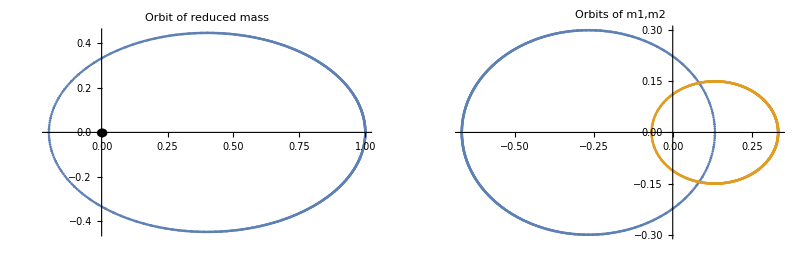

```mathematica
Remove["Global`*"]

m1=1;m2=2;x0=1;y0=0;vx0=0;vy0=1;

sol=NDSolve[{x''[t]==-(m1+m2)*x[t]/((x[t]^2+y[t]^2)^(3/2)),y''[t]==-(m1+m2)*y[t]/((x[t]^2+y[t]^2)^(3/2)),x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,10}];
x1=x/.sol[[1]];
y1=y/.sol[[1]];
xyList=Table[{x1[t],y1[t]},{t,0,10,.01}];

gr1=Show[ListPlot[xyList],Graphics[Disk[{0,0},.02]],BaseStyle->FontSize->15,PlotLabel->"Orbit of reduced mass"];

gr2=ListPlot[{-m2/(m1+m2)*xyList,m1/(m1+m2)*xyList},
BaseStyle->FontSize->15,PlotLabel->"Orbits of m1,m2"];

GraphicsGrid[{{gr1,gr2}}]
```

## Example 9.2

```mathematica
Remove["Global`*"]

rr=k*θ;
force=-(l^2/(μ*rr^2)*(D[1/rr,{θ,2}]+1/rr));

Print["The force is:  F(r) = " ,force/.{θ->r/k}//FullSimplify];
Print[]

soln=DSolve[{θ'[t]==l/(μ*k^2*θ[t]^2),θ[0]==0},θ[t],t][[2]][[1]];

Print["The positive solution of the ODE is: "];
Print[" θ[t] = ",θ[t]/.soln];
Print["or"];
Print["θ[t]^3 = ",(θ[t]/.soln)^3]
```

The force is:  F(r) = -(l^2 (2 k^2+r^2))/(r^5 μ)

The positive solution of the ODE is:

θ[t] = (3^(1/3) l^(1/3) t^(1/3))/(k^(2/3) μ^(1/3))

or

θ[t]^3 = (3 l t)/(k^2 μ)

## Example 9.4

The eccentricity of Earth is  e = 0.0169943

The eccentricity of Mercury is  e = 0.206897

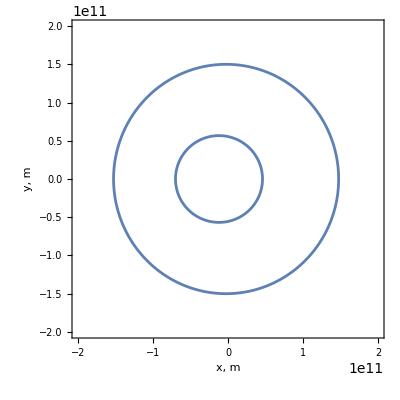

```mathematica
Remove["Global`*"]

rminE=147.5*10^6*10^3;
rmaxE=152.6*10^6*10^3;

a=(rminE+rmaxE)/2;
eEarth=(rmaxE-rminE)/(rminE+rmaxE)//N;
Print["The eccentricity of Earth is  e = ",eEarth];

gr1=PolarPlot[a*(1-eEarth^2)/(1+eEarth*Cos[θ]),{θ,0,2*Pi},Frame->True,FrameLabel->{"x, m","y, m"},PlotRange->{{-2*10^11,2*10^11},{-2*10^11,2*10^11}}];

rminM=46*10^6*10^3;
rmaxM=70*10^6*10^3;

a=(rminM+rmaxM)/2;
eMercury=(rmaxM-rminM)/(rminM+rmaxM)//N;
Print["The eccentricity of Mercury is  e = ",eMercury];

gr2=PolarPlot[a*(1-eMercury^2)/(1+eMercury*Cos[θ]),{θ,0,2*Pi},Frame->True,PlotRange->{{-2*10^11,2*10^11},{-2*10^11,2*10^11}}];

Show[{gr1,gr2},BaseStyle->FontSize->16]
```

## Example 9.5

```mathematica
Remove["Global`*"]

Print["All quantities are in SI units"];
perigee=0.3633*10^9;
apogee=0.4055*10^9;
e=(apogee-perigee)/(apogee+perigee);a=(perigee+apogee)/2;

Print["semimajor axis a = ",a];
Print[]

Print["Eccentricity of moon's orbit = ",e];
Mmoon=0.07346*10^24;
Mearth=5.9724*10^24;
G=6.673*10^-11;

Period=Sqrt[4*Pi^2*a^3/(G*(Mmoon+Mearth))];
Print["The Revolution period T of moon = ",Period/(3600*24)," days"];
```

All quantities are in SI units

semimajor axis a = 3.844×10^8

Eccentricity of moon's orbit = 0.0548907

The Revolution period T of moon = 27.2867 days

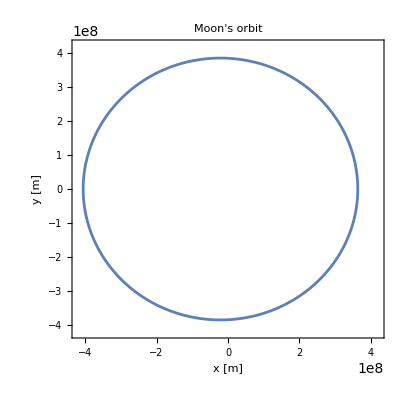

```mathematica
α=a*(1-e^2);
r=α/(1+e*Cos[θ]);

PolarPlot[r,{θ,0,2*Pi},FrameLabel->{"x [m]","y [m]"},Frame->True,BaseStyle->{FontSize->16},PlotLabel->"Moon's orbit",PlotRange->{{-4.2*10^8,4.2*10^8},{-4.2*10^8,4.2*10^8}}]
```

## Example 9.7

```mathematica
Remove["Global`*"]

G=6.67408*10^-11 ;
aValues={421700,671034,1070412,1882709}*10^3;
periods={1.7691,3.5512,7.1546,16.689}*3600*24;
list=Transpose[{aValues^3,periods^2}];

gr1=ListPlot[list,Frame->True,FrameLabel->{"a^3 (m^3)","P^2  (s^2)"},BaseStyle->FontSize->17,PlotRange->{{0,8*10^27},{0,2.2*10^12}},PlotMarkers->Automatic];

Print["Best line fit = a+b*x  with "];
bestline=FindFit[list,a+b*x,{a,b},x];
Print["Best slope =",slope=b/.bestline];
Print[]

mJupiter=NSolve[slope==4*Pi^2/(G*M),M];
Print["Mass of Jupiter = ",M/.mJupiter[[1]]," kg"];
Print[]

gr2=Plot[(a+b*x)/.bestline,{x,0,8*10^27},BaseStyle->FontSize->17,Frame->True,PlotRange->{{0,8*10^27},{0,2.2*10^12}}];
Show[gr1,gr2]
```

Best line fit = a+b*x  with

Best slope =3.11558×10^-16

Mass of Jupiter = 1.89859×10^27 kg

-Graphics-